# Precession of magnetar

## 1. The dynamics of magnetar precession

## Time scale estimation

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;
c=29979245800.0;
Ms=1.988409870698051*10^33;
km=10^5;
R=10*km;
M=1.4*Ms;
Is=2/5*M*R^2;
P=1;k=0.6;B=10^14;
ω=(2 π)/P;
m=(B R^3)/2;
τc=(3 c^3 Is)/((2 m^2) ω^2)
τa=(2 R ω τc)/((3 k) c)
ϵp=(3 B^2 R^5)/(20 (Is c^2))
```

4.55982×10^11

1.06185×10^8

1.49884×10^-9

```mathematica
I1=I0;I2=I1 (1+ϵ1);I3=I1 (1+ϵ);
Ib=DiagonalMatrix[{I1,I2,I3}];
Ω={ω0*u1[t], ω0*u2[t], ω0*u3[t]};
p={m*Sin[χ]Cos[η],m Sin[χ]Sin[η],m Cos[χ]};
T1=(2 ω0^2*u[t]^2)/(3 c^3)Cross[Cross[Ω,p],p];
T2=k/(R c^2)Dot[Ω,p]*Cross[Ω,p];
```

## The numerical integration of radiative precession

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
Radiative[ϵ_,P_,B_,k_,M_,R_,χ_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;ϵm=(3 B^2 R^5)/(20 (I0 c^2));
sol=NDSolve[{u1'[t]==-(u2[t]*u3[t])/τp+(k m^2 ω0 Cos[χ] u2[t] (Sin[χ] u1[t]+Cos[χ] u3[t]))/(c^2 I0 R),u2'[t]==(u1[t] u3[t])/τp-(k m^2 ω0 (Sin[χ] u1[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Sin[χ] u3[t]))/(c^2 I0 R), u3'[t]==-(k m^2 ω0 Sin[χ] u2[t] (Sin[χ] u1[t]+Cos[χ] u3[t]))/(c^2 I0 R(1+ϵ)),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,100*τp},Method->"ExplicitRungeKutta"]
; sol]

effective[ϵ_,P_,B_,k_,M_,R_,χ_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0,I0(1+ϵ)}];
m={Sin[χ],0,Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;

h=UnitStep[Leff2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={a*JacobiCN[t*ωp,k2],a*(1+e)^0.5 JacobiSN[t*ωp,k2],b*JacobiDN[t*ωp,k2]},h==0,sol={a*JacobiDN[t*ωp*k2^0.5,1/k2],b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2],b*JacobiCN[t*ωp*k2^0.5,1/k2]}];{sol}];
ϵ=1.0*10^-7;P=2;B=5*10^14;k=0.6;M=1.4*Ms;R=10.0*km;χ=45.0/180*π;θ=15/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0,I0(1+ϵ)}];
m={Sin[χ],0,Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;
T=(4*Ieff3)/((Ieff3-Ieff1)/Ieff3 * Leff2^0.5)*((1+e)/(ωeff3/ω00)^2)^0.5 EllipticK[k2];
SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,P,0,k,M,R,χ,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,2*T,2T/300}];
free=Transpose@{time,ux,uy,uz};
Export["free.dat",free];
SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,P,B,k,M,R,χ,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,2*T,2T/300}];
real=Transpose@{time,ux,uy,uz};
Export["real.dat",real];
time=Table[t,{t,0,2T,2T/300}];
trans=Table[0,Length[time],3];
For[i=1,i≤Length[time],i++,
trans[[i]]=Flatten[{time[[i]],effective[ϵ,P,B,k,M,R,χ,θ,time[[i]]]}]];
Export["trans.dat",trans];
```

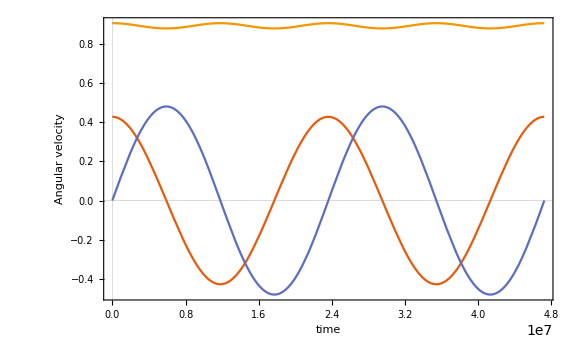

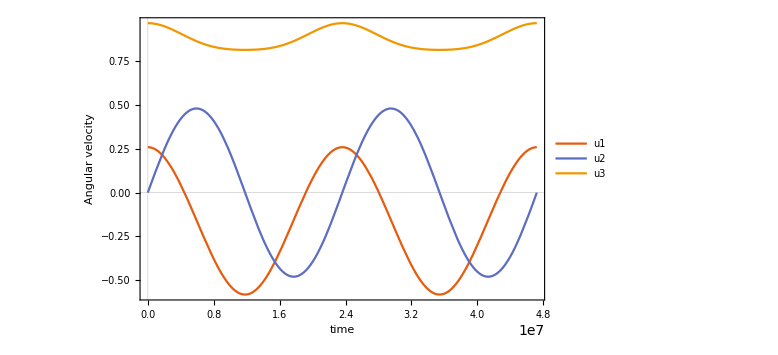

```mathematica
SetDirectory[NotebookDirectory[]];
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
effective[ϵ_,P_,B_,k_,M_,R_,χ_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0,I0(1+ϵ)}];
m={Sin[χ],0,Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;

h=UnitStep[Leff2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={a*JacobiCN[t*ωp,k2],a*(1+e)^0.5 JacobiSN[t*ωp,k2],b*JacobiDN[t*ωp,k2]},h==0,sol={a*JacobiDN[t*ωp*k2^0.5,1/k2],b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2],b*JacobiCN[t*ωp*k2^0.5,1/k2]}];{sol}];
ϵ=1.0*10^-7;P=2;B=5*10^14;k=0.6;M=1.4*Ms;R=10.0*km;χ=45.0/180*π;θ=15/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0,I0(1+ϵ)}];
m={Sin[χ],0,Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;
T=(4*Ieff3)/((Ieff3-Ieff1)/Ieff3 * Leff2^0.5)*((1+e)/(ωeff3/ω00)^2)^0.5 EllipticK[k2];
Plot[{Evaluate[effective[ϵ,P,B,k,M,R,χ,θ,t]]},{t,0,2T},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White]

sol=Evaluate[Radiative[1*10^-7,2,5*10^14,0.6,1.4*Ms,10*km,45/180*π,15/180*π]];
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,2T},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]

(*ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,2T,2*T/300}];
trans=Transpose@{time,ux,uy,uz};
Export["trans.dat",trans];*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
effective[ϵ_,P_,B_,k_,M_,R_,χ_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0,I0(1+ϵ)}];
m={Sin[χ],0,Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;

h=UnitStep[Leff2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={a*JacobiCN[t*ωp,k2],a*(1+e)^0.5 JacobiSN[t*ωp,k2],b*JacobiDN[t*ωp,k2]},h==0,sol={a*JacobiDN[t*ωp*k2^0.5,1/k2],b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2],b*JacobiCN[t*ωp*k2^0.5,1/k2]}];{sol}];
ϵ=1.0*10^-7;P=2;B=5*10^14;k=0.6;M=1.4*Ms;R=10.0*km;χ=45.0/180*π;θ=15/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0,I0(1+ϵ)}];
m={Sin[χ],0,Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;
T=(4*Ieff3)/((Ieff3-Ieff1)/Ieff3 * Leff2^0.5)*((1+e)/(ωeff3/ω00)^2)^0.5 EllipticK[k2];
Plot[{Evaluate[effective[ϵ,P,B,k,M,R,χ,θ,t]]},{t,0,2T},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White]

sol=Evaluate[Radiative[1*10^-7,2,5*10^14,0.6,1.4*Ms,10*km,45/180*π,15/180*π]];
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,2T},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

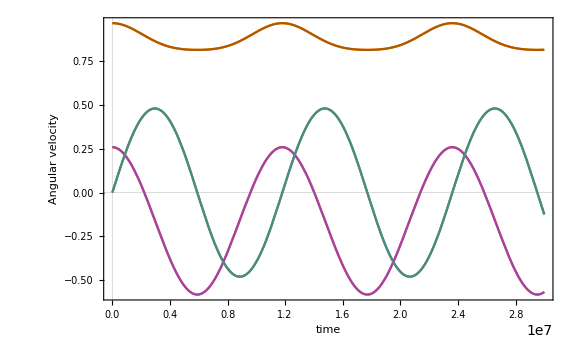

0.

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
effective[ϵ_,P_,B_,k_,M_,R_,χ_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0,I0(1+ϵ)}];
m={Sin[χ],0,Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;

h=UnitStep[Leff2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={a*JacobiCN[t*ωp,k2]*(e1eff.e1)+a*(1+e)^0.5 JacobiSN[t*ωp,k2]*(e2eff.e1)+b*JacobiDN[t*ωp,k2]*(e3eff.e1),a*JacobiCN[t*ωp,k2]*(e1eff.e2)+a*(1+e)^0.5 JacobiSN[t*ωp,k2]*(e2eff.e2)+b*JacobiDN[t*ωp,k2]*(e3eff.e2),a*JacobiCN[t*ωp,k2]*(e1eff.e3)+a*(1+e)^0.5 JacobiSN[t*ωp,k2]*(e2eff.e3)+b*JacobiDN[t*ωp,k2]*(e3eff.e3)},h==0,sol={a*JacobiDN[t*ωp*k2^0.5,1/k2]*(e1eff.e1)+b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2]*(e2eff.e1)+b*JacobiCN[t*ωp*k2^0.5,1/k2]*(e3eff.e1),a*JacobiDN[t*ωp*k2^0.5,1/k2]*(e1eff.e2)+b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2]*(e2eff.e2)+b*JacobiCN[t*ωp*k2^0.5,1/k2]*(e3eff.e2),a*JacobiDN[t*ωp*k2^0.5,1/k2]*(e1eff.e3)+b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2]*(e2eff.e3)+b*JacobiCN[t*ωp*k2^0.5,1/k2]*(e3eff.e3)}];{sol}]
Radiative[ϵ_,P_,B_,k_,M_,R_,χ_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;ϵm=(3 B^2 R^5)/(20 (I0 c^2));
sol=NDSolve[{u1'[t]==-(u2[t]*u3[t])/τp+(k m^2 ω0 Cos[χ] u2[t] (Sin[χ] u1[t]+Cos[χ] u3[t]))/(c^2 I0 R),u2'[t]==(u1[t] *u3[t])/τp-(k m^2 ω0 (Sin[χ] u1[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Sin[χ] u3[t]))/(c^2 I0 R), u3'[t]==-(k m^2 ω0 Sin[χ] u2[t] (Sin[χ] u1[t]+Cos[χ] u3[t]))/(c^2 I0 R(1+ϵ)),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,100*τp},Method->"ExplicitRungeKutta"]
; sol]

Plot[{Evaluate[effective[1.0*10^-7,1,5*10^14,0.6,1.4*Ms,10.0*km,45.0/180*π,15/180.0*π,t]],Evaluate[{u1[t],u2[t],u3[t]}/.Radiative[1*10^-7,1,5*10^14,0.6,1.4*Ms,10*km,45/180*π,15/180*π]]},{t,0,3*10^7},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White]
Print[ωeff2]
```

## Triaxial case

```mathematica
Remove["Global`*"]
Ω={ω0*u1[t], ω0*u2[t], ω0*u3[t]};
p={m*Sin[χ]Cos[η],m Sin[χ]Sin[η],m Cos[χ]};
T2=Simplify[k/(R c^2)Dot[Ω,p]*Cross[Ω,p]/ω0/I0]
```

{1/(c^2 I0 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),-1/(c^2 I0 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]),1/(c^2 I0 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t])}

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

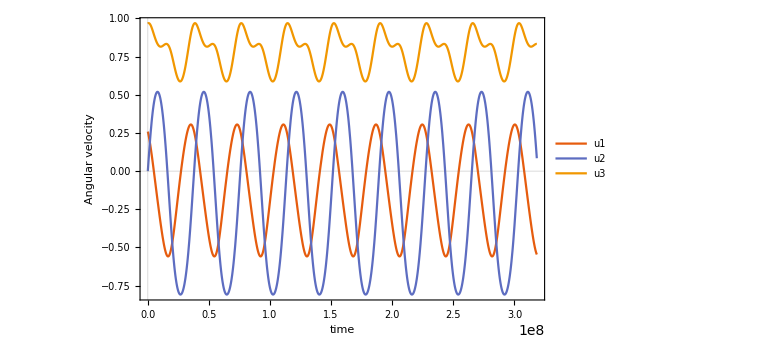

```mathematica
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]
ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=2;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=30.0/180*π;
θ=15/180.0*π;
τp=1/ω0/ϵ;

sol=Evaluate[Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,100*τp},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

-0.488013

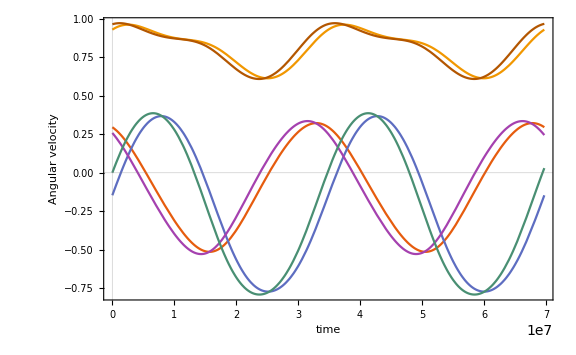

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
effective[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;

h=UnitStep[Leff2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={a*JacobiCN[t*ωp,k2]*(e1eff.e1)+a*(1+e)^0.5 JacobiSN[t*ωp,k2]*(e2eff.e1)+b*JacobiDN[t*ωp,k2]*(e3eff.e1),a*JacobiCN[t*ωp,k2]*(e1eff.e2)+a*(1+e)^0.5 JacobiSN[t*ωp,k2]*(e2eff.e2)+b*JacobiDN[t*ωp,k2]*(e3eff.e2),a*JacobiCN[t*ωp,k2]*(e1eff.e3)+a*(1+e)^0.5 JacobiSN[t*ωp,k2]*(e2eff.e3)+b*JacobiDN[t*ωp,k2]*(e3eff.e3)},h==0,sol={a*JacobiDN[t*ωp*k2^0.5,1/k2]*(e1eff.e1)+b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2]*(e2eff.e1)+b*JacobiCN[t*ωp*k2^0.5,1/k2]*(e3eff.e1),a*JacobiDN[t*ωp*k2^0.5,1/k2]*(e1eff.e2)+b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2]*(e2eff.e2)+b*JacobiCN[t*ωp*k2^0.5,1/k2]*(e3eff.e2),a*JacobiDN[t*ωp*k2^0.5,1/k2]*(e1eff.e3)+b*(1+1/e)^0.5 JacobiSN[t*ωp*k2^0.5,1/k2]*(e2eff.e3)+b*JacobiCN[t*ωp*k2^0.5,1/k2]*(e3eff.e3)}];{sol}]
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]

ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=2;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45/180*π;
θ=15/180.0*π;
τp=1/ω0/ϵ;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Print[ωeff2]
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;

T=(4*Ieff3)/((Ieff3-Ieff1)/Ieff3 * Leff2^0.5)*((1+e)/(ωeff3/ω00)^2)^0.5 EllipticK[k2];

(*Plot[{Evaluate[effective[ϵ,ϵ1,P,B,k,M,R,χ,η,θ,t]],Evaluate[{u1[t],u2[t],u3[t]}/.Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ]]},{t,0,2T},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White]*)
```

```mathematica
ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=2;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=15/180.0*π;
τp=1/ω0/ϵ;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;
e=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;
ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;

T=(4*Ieff3)/((Ieff3-Ieff1)/Ieff3 * Leff2^0.5)*((1+e)/(ωeff3/ω00)^2)^0.5 EllipticK[k2];

SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,ϵ1,P,0,k,M,R,χ,η,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,2*T,T/300}];
free=Transpose@{time,ux,uy,uz};
Export["free.dat",free];
SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,P,B,k,M,R,χ,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,T,T/300}];
real=Transpose@{time,ux,uy,uz};
Export["real.dat",real];
time=Table[t,{t,0,2T,2T/300}];
trans=Table[0,Length[time],3];
For[i=1,i≤Length[time],i++,
trans[[i]]=Flatten[{time[[i]],effective[ϵ,P,B,k,M,R,χ,θ,time[[i]]]}]];
Export["trans.dat",trans];
```

```mathematica
InverseJacobiSN[0,0.3]
```

0.

```mathematica
ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=2;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=15/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Leff2=Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
```